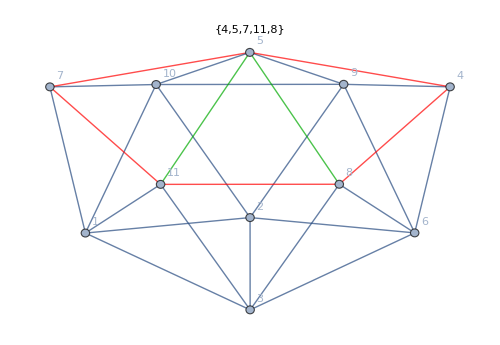
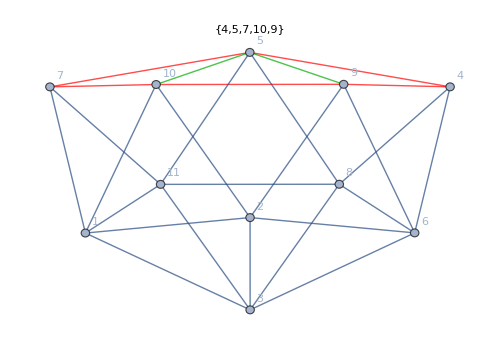
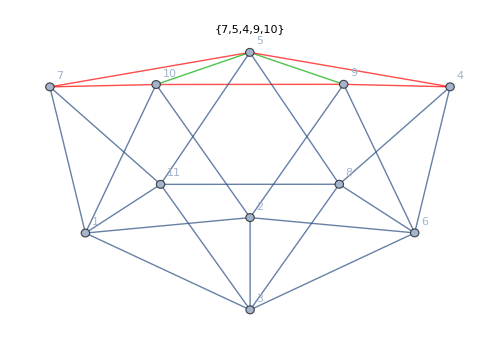
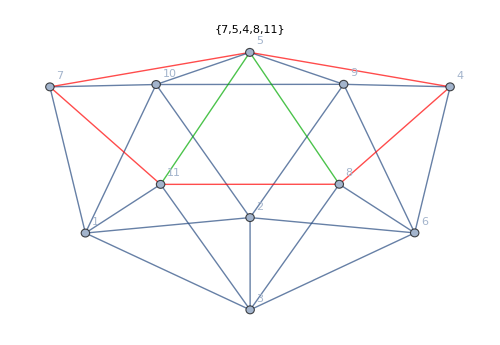

```mathematica
Map[
Graph[ReadGrof[#[[1]]], VertexLabels->"Name", GraphLayout->"SpringElectricalEmbedding",EdgeStyle->
Join[
Map[#->Red&,Rule3Cycle[#[[3,2]]]],
Map[#->Darker[Green]&,#[[3,3]]]
], GraphHighlightStyle->"VertexDiamond", ImageSize->500, PlotLabel->#[[3,2]]]&,
Join[Select[deps3,#[[2]]==6985&],Select[deps3Bis,#[[2]]==6985&]]
]
```

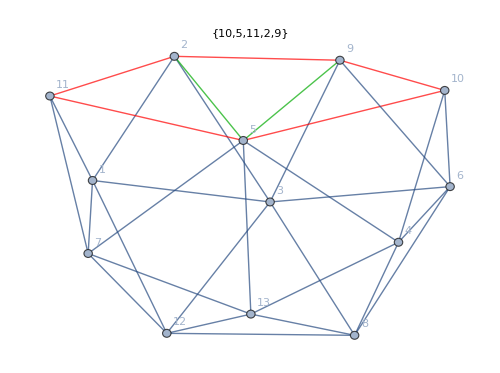
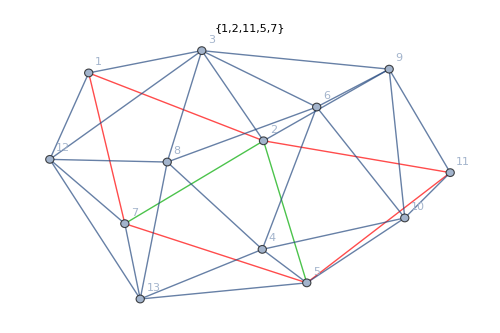
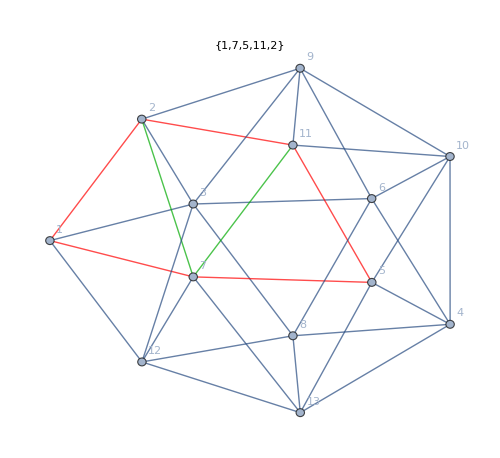
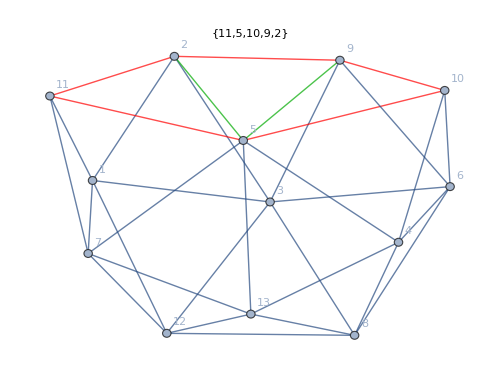
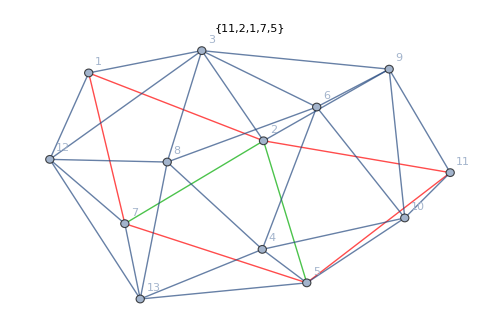
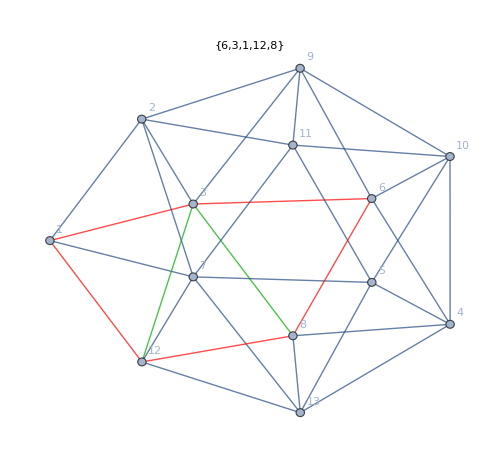
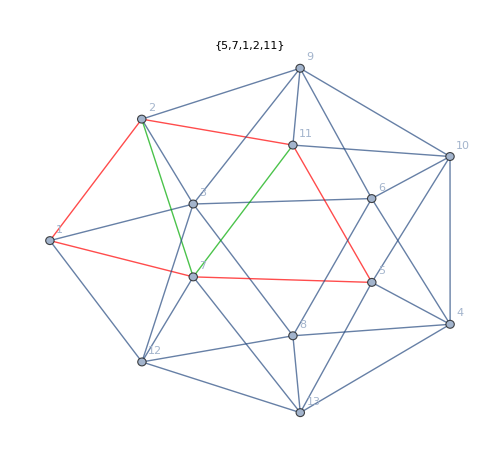
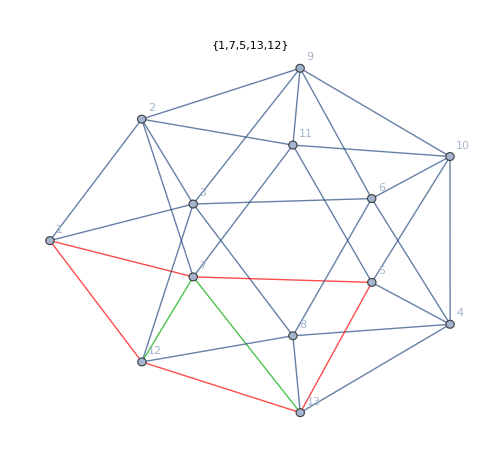

```mathematica
Map[
Graph[ReadGrof[#[[1]]], VertexLabels->"Name", GraphLayout->"SpringElectricalEmbedding",EdgeStyle->
Join[
Map[#->Red&,Rule3Cycle[#[[3,2]]]],
Map[#->Darker[Green]&,#[[3,3]]]
], GraphHighlightStyle->"VertexDiamond", ImageSize->500,PlotLabel->#[[3,2]]]&,
Join[Select[deps3,#[[2]]==279676&],Select[deps3Bis,#[[2]]==279676&]]
]
```